```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

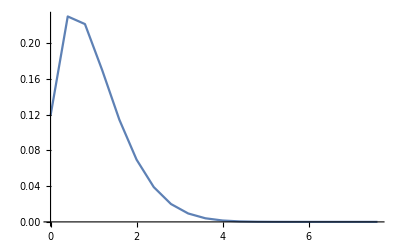

```mathematica
susceptibilityBins=20;
susceptibilityInitialPopulations=Module[{mean=.15, stdDev=.1, a, b, binSize,betaDist,temp},
  a = mean(mean-mean^2+stdDev^2)/stdDev^2;
  b = (mean-1)(mean^2-mean-stdDev^2)/stdDev^2;
  binSize=1./susceptibilityBins;
  betaDist=CDF[BetaDistribution[a,b]];
  N[Table[betaDist[binSize*i]-betaDist[binSize*(i-1)],{i,1,susceptibilityBins}]]
];
susceptibilityCoefficient=1./Total[susceptibilityValues*susceptibilityInitialPopulations];

ListLinePlot[Transpose[{susceptibilityValues,susceptibilityInitialPopulations}],PlotRange->All]
```

Fitting model for CA

>> <|chiSquared→0.105852,rmsRelativeError→24.3919,rmsRelativeErrorDeaths→16.6783,rmsRelativeErrorPcr→29.0063,meanRelativeErrorDeaths→-14.1442,meanRelativeErrorPcr→-23.0227,rSquaredDeaths→1272.43,rSquaredPcr→3290.47,deathResidual7Day→-5.86494,pcrResidual7Day→43.1767|>

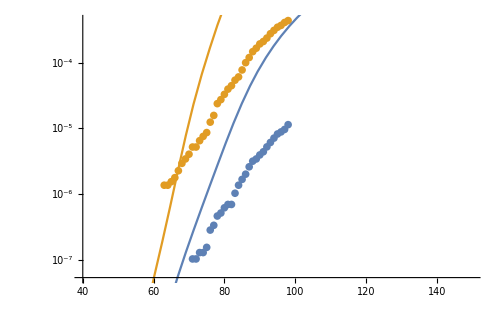
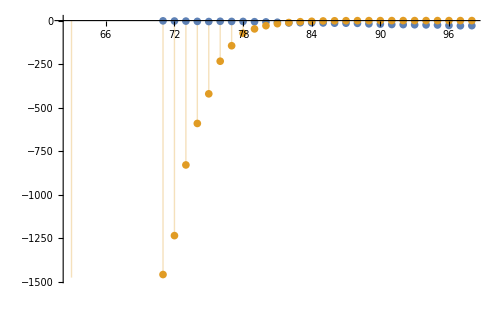
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.10003 | 0.382822 | 8.09785 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[8.09785,60.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 53.9979 | 1.6462 | 32.8016 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[32.8016,60.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 1.6974 | 0.398277 | 4.26187 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[4.26187,60.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.82765 | 0.296324 | 6.16772 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[6.16772,60.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | -1.55398×10^-6 | -3.88495×10^-7
Error | 60 | 1.55486×10^-6 | 2.59143×10^-8
Uncorrected Total | 64 | 8.75974×10^-10 | 
Corrected Total | 63 | 8.5923×10^-10 |

>> Current scenario Generating simulations for CA in the

>> Generating simulations for CA in the  Italy scenario

>> Generating simulations for CA in the  Wuhan scenario

>> Generating simulations for CA in the  Normal scenario

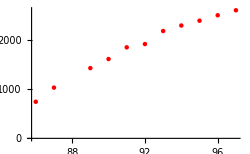
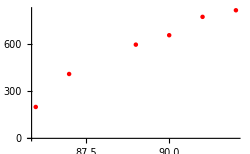
>> Current Hospitalizations for CA
-Graphics-Cumulative Hospitalizations for CA
-Graphics-Current ICU for CA
-Graphics-Cumulative ICU for CA
-Graphics-

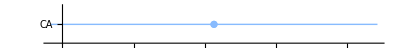
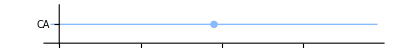
Currently Hospitalized
-Graphics- | Cumulative Hospitalized
-Graphics- | Currently ICU
-Graphics- | Cumulative ICU
-Graphics-

state | distancingLevel | id | distancingDays | maintain | name | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences"} |  | 
CA | 81/140 | scenario1 | 90 | True | Current | 295691. | 5.00163×10^6 | 2.56998×10^7 | 0.659259 | 0.0115056 | 0.0164365 | 0.0591189 | 0.278025 | - | Wed 25 Mar 2020 04:50:09 | Sat 28 Mar 2020 22:24:07 | 3.10003 | 53.9979 | 1.6974
CA | 0.4 | scenario2 | 90 | False | Italy | 262561. | 5.54463×10^6 | 2.68566×10^7 | 0.688933 | 0.0097764 | 0.0139663 | 0.047354 | 0.294934 | - | Wed 25 Mar 2020 04:50:09 | Sat 28 Mar 2020 22:24:07 | 3.10003 | 53.9979 | 1.6974
CA | 0.11 | scenario3 | 60 | False | Wuhan | 129861. | 2.05759×10^6 | 1.37587×10^7 | 0.352944 | 0.00943842 | 0.0134835 | 0.0631131 | 0.21364 | Sat 13 Jun 2020 10:09:26 | Wed 25 Mar 2020 04:50:09 | Sat 28 Mar 2020 22:24:07 | 3.10003 | 53.9979 | 1.6974
CA | 1 | scenario4 | 90 | False | Normal | 295518. | 5.76813×10^6 | 3.07986×10^7 | 0.790055 | 0.00959517 | 0.0137074 | 0.0512328 | 0.267551 | - | Wed 25 Mar 2020 04:50:09 | Sat 28 Mar 2020 22:24:07 | 3.10003 | 53.9979 | 1.6974

```mathematica
asd=GenerateModelExport[10,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```

```mathematica
TableForm[Import["tests/summary.csv"]]
```

state | distancingLevel | id | distancingDays | maintain | name | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences"} |  | 
CA | 81/140 | scenario1 | 90 | True | Current | 333219. | 8.03111×10^6 | 3.20231×10^7 | 0.821466 | 0.0104056 | 0.0148651 | 0.0414909 | 0.358274 | - | Fri 15 May 2020 01:37:04 | Sat 13 Jun 2020 18:28:00 | 3.27233 | 52.9291 | 1.60069
CA | 0.4 | scenario2 | 90 | False | Italy | 335358. | 9.62571×10^6 | 3.47351×10^7 | 0.891035 | 0.00965475 | 0.0137925 | 0.0348399 | 0.395883 | - | Sat 8 Aug 2020 19:58:32 | Thu 13 Aug 2020 10:39:32 | 3.27233 | 52.9291 | 1.60069
CA | 0.11 | scenario3 | 60 | False | Wuhan | 5062.67 | 79452. | 514890. | 0.0132081 | 0.00983253 | 0.0140465 | 0.0637198 | 0.220441 | Tue 26 May 2020 09:28:13 | - | - | 3.27233 | 52.9291 | 1.60069
CA | 1 | scenario4 | 90 | False | Normal | 307610. | 6.32762×10^6 | 3.36277×10^7 | 0.862629 | 0.00914752 | 0.0130679 | 0.0486139 | 0.26881 | - | Tue 28 Apr 2020 12:41:28 | Sun 3 May 2020 08:52:06 | 3.27233 | 52.9291 | 1.60069

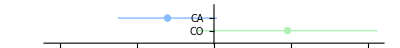

```mathematica
exportAllStatesHospitalizationGoodnessOfFitMetricsSvg["",asd]
```

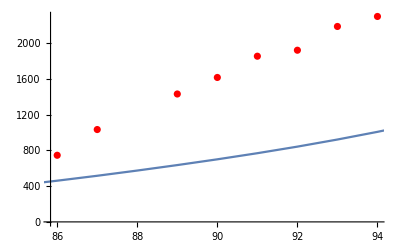

```mathematica
plotStateHospitalization[asd["CA"]]
```